# Fisher Matrix for multiple tracers

Raul Abramo and Luca Amendola  arXiv : xxxx.yyyy

This notebook produces the model-independent Fisher matrix (per unit phase-space volume) for the band power-spectrum P and the redshift distortion parameter beta, for a single tracer, and, similarly, for P_(1,2) and beta_(1,2)  for two tracers. The parameters are actually the log of these quantities, so the output gives directly the relative errors. In particular, the notebook plots the relative, marginalized error on the redshift distortion parameter beta, both for the single- and the two-tracer case. This should correspond to Fig. 1 of the paper. The entire notebook runs in less than 5 minutes on a laptop.

```mathematica
SetDirectory[NotebookDirectory[]]
```

## Single tracer

```mathematica
(* all spectra in units of noise*bias^2; log beta as parameter *)
```

```mathematica
Clear[p11,p12,p22,p34,p23,m];faca=(1+betaa*mu^2);

ppar={pa,betaa};

npar=Length[ppar];

na=1+1/faca^2/pa; 

(* correlation matrix *)

 c=Simplify[{{0,faca^2*pa*na},{faca^2*pa*na,0}}];

c//TableForm

n=Length[c];gamma=Simplify[Table[Inverse[c][[i,m]]*Inverse[c][[j,l]],{i,n},{j,n},{l,n},{m,n}]];

(* analytical fisher matrix *)

fisher=Simplify[PowerExpand[Simplify[(1/2)*Table[Integrate[Simplify[Sum[ppar[[a]]*ppar[[b]]*D[c[[i,j]],ppar[[a]]]*D[c[[l,m]],ppar[[b]]]*gamma[[i,j,l,m]],{i,n},{j,n},{l,n},{m,n}]],{mu,-1,1},GenerateConditions->False]/2,{a,npar},{b,npar}]]]];fisher//TableForm

 (* analytical relative error on beta_1 *)

Clear[errbeta1];errbeta1[pa_,betaa_]=Simplify[Inverse[fisher][[2,2]]];
```

## Two tracers

```mathematica
Clear[p11,p12,p22,p34,p23,m];faca=(1+betaa*mu^2);facb=(1+betab*mu^2);

p34=pb;

ppar={pa,pb,betaa,betab};

npar=Length[ppar];

na=1+1/faca^2/pa;nb=1+1/facb^2/pb;
c={{0,faca^2*pa*na,0,faca*facb*Sqrt[pa*pb]},{faca^2*pa*na,0,faca*facb*Sqrt[pa*pb],0},{0,faca*facb*Sqrt[pa*pb],0,facb^2*p34*nb},{faca*facb*Sqrt[pa*pb],0,facb^2*p34*nb,0}};


n=Length[c];gamma=Simplify[Table[Inverse[c][[i,m]]*Inverse[c][[j,l]],{i,n},{j,n},{l,n},{m,n}]];

(* numerical fisher matrix *)

Clear[fmu,betaa,betab,pa,pb];fmu[betaa_,betab_,pa_,pb_]=Table[Simplify[Sum[ppar[[a]]*ppar[[b]]*D[c[[i,j]],ppar[[a]]]*D[c[[l,m]],ppar[[b]]]*gamma[[i,j,l,m]],{i,n},{j,n},{l,n},{m,n}]],{a,npar},{b,npar}];

fishern[betaa_,betab_,pa_,pb_]:=Table[1/2*NIntegrate[fmu[betaa,betab,pa,pb][[a,b]],{mu,-1,1}]/2,{a,npar},{b,npar}];

 (* numerical relative error on beta_1 *)

errbeta2[betaa_,betab_,pa_,pb_]:=Inverse[fishern[betaa,betab,pa,pb]][[3,3]];
```

```mathematica
(* quick check: this should give 23.2418 *)

errbeta2[1,1,1,1]
```

```mathematica
(* this plot should produce Fig. 1 of the paper *)
```

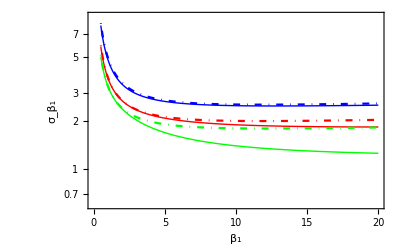

```mathematica
LogPlot[{Sqrt[Chop[errbeta2[ba,1.,1.,1.]]],Sqrt[Chop[errbeta2[ba,1.,3.,3.]]],Sqrt[Chop[errbeta2[ba,1.,10.,10.]]],Sqrt[Chop[errbeta1[1,ba]]],Sqrt[Chop[errbeta1[3,ba]]],Sqrt[Chop[errbeta1[10,ba]]]},{ba,.5,20},PlotStyle->{{Blue,Thick},{Red,Thick},{Green,Thick},{Blue,DotDashed},{Red,DotDashed},{Green,DotDashed}},PlotRange->{.6,9},Frame->True,FrameLabel->{Subscript[β, 1],Subscript[σ, Subscript[β, 1]]},BaseStyle->{16,FontFamily->"Times"}]
```